```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];
(*Latex dictionary*)
Format[mu]:=μ;Format[muP]:=Subscript[μ,P];
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[ga12]:=Subscript[γ,12];Format[ga2]:=Subscript[γ,21];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[th3]:=Subscript[θ,12];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[LaP]:=Subscript[Λ,p];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[be12]:=Subscript[β,12];Format[be21]:=Subscript[β,21];
Format[de1]:=Subscript[δ,1];Format[de2]:=Subscript[δ,2];
Format[de12]:=Subscript[δ,12];Format[de21]:=Subscript[δ,21];
Format[deS]:=Subscript[δ,s];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];
Format[mu12]:=Subscript[μ,12];Format[mu21]:=Subscript[μ,21];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];Format[si]:=σ;Format[rh]:=ρ;
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];Format[i21]:=Subscript[i,21];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];Format[r12]:=Subscript[r,12];
(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)RN={(*epidemic reactions:12 total*)"S"+"I1"->2*"I1","S"+"I21"->"I1"+"I21","S"+"I2"->2*"I2","S"+"I12"->"I2"+"I12","R1"+"I2"->"I12"+"I2","R1"+"I12"->2*"I12","R2"+"I1"->"I21"+"I1","R2"+"I21"->2*"I21","I1"->"R1","I2"->"R2","I12"->"R12","I21"->"R12",(*"I1"->"D","I2"->"D","I12"->"D","I21"->"D",*)(*ecological reactions:16 total*)0->"S","S"->0,"R1"->0,"R2"->0,"R12"->0,0->"P","P"->0,"I1"->0,"I2"->0,"I12"->0,"I21"->0,"P"+"S"->2*"P","P"+"I1"->2*"P","P"+"I2"->2*"P","P"+"I12"->2*"P","P"+"I21"->2*"P"};
rts={(*epidemic transitions*)be1*s*i1,be1*s*i21,be2*s*i2,be2*s*i12,be12*r1*i2,be12*r1*i12,be21*r2*i1,be21*r2*i21,ga1*i1,ga2*i2,ga12*i12,ga21*i21,(*mu1*i1,mu2*i2,mu12*i12,mu21*i21,*)(*ecological transitions*)La,(*inflow 0->s*)mu*s,(*natural loss of s*)mu*r1,mu*r2,mu*r12,LaP,(*inflow 0->p*)muP*p,(*natural loss of p*)mu1*i1,mu2*i2,mu12*i12,mu21*i21,deS*p*s,(*predation on s*)de1*p*i1,(*predation on i1*)de2*p*i2,(*predation on i2*)de12*p*i12,(*predation on i12*)de21*p*i21     (*predation on i21*)};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy,cDFE, E0, K, R0A, infV, alp, 
  bet, gam, ngm} = bdAn[RN, rts];
Print["RHS=",RHS//FullSimplify//MatrixForm,"mSi=",mSi,"E0=",E0," K= ",K//MatrixForm,"where the order is ",infV," after permutation ",K[[{1,4,2,3},{1,4,2,3}]]//MatrixForm, "the repr. funs are",R0A];
```

reactions and transitions: (I1+S→2 I1 | β_1 i_1 s
I21+S→I1+I21 | β_1 i_21 s
I2+S→2 I2 | β_2 i_2 s
I12+S→I12+I2 | β_2 i_12 s
I2+R1→I12+I2 | β_12 i_2 r_1
I12+R1→2 I12 | β_12 i_12 r_1
I1+R2→I1+I21 | β_21 i_1 r_2
I21+R2→2 I21 | β_21 i_21 r_2
I1→R1 | γ_1 i_1
I2→R2 | γ_21 i_2
I12→R12 | γ_12 i_12
I21→R12 | ga21 i_21
0→S | Λ
S→0 | μ s
R1→0 | μ r_1
R2→0 | μ r_2
R12→0 | μ r_12
0→P | Λ_p
P→0 | μ_P p
I1→0 | i_1 μ_1
I2→0 | i_2 μ_2
I12→0 | i_12 μ_12
I21→0 | i_21 μ_21
P+S→2 P | δ_s p s
I1+P→2 P | δ_1 i_1 p
I2+P→2 P | δ_2 i_2 p
I12+P→2 P | δ_12 i_12 p
I21+P→2 P | δ_21 i_21 p)

RHS=(-i_1 (γ_1+μ_1+δ_1 p)+β_1 (i_1+i_21) s
Λ-(β_2 (i_12+i_2)+β_1 (i_1+i_21)+μ+δ_s p) s
-i_21 (ga21+μ_21+δ_21 p)+β_21 (i_1+i_21) r_2
-i_2 (γ_21+μ_2+δ_2 p)+β_2 (i_12+i_2) s
-i_12 (γ_12+μ_12+δ_12 p)+β_12 (i_12+i_2) r_1
γ_1 i_1-(β_12 (i_12+i_2)+μ) r_1
γ_21 i_2-(β_21 (i_1+i_21)+μ) r_2
γ_12 i_12+ga21 i_21-μ r_12
Λ_p+p (δ_1 i_1+δ_12 i_12+δ_2 i_2+δ_21 i_21-μ_P+δ_s s))mSi={{i1,i21},{i2,i12}}E0={{p→(δ_s Λ+δ_s Λ_p-μ μ_P+√(4 δ_s Λ_p μ μ_P+(δ_s Λ+δ_s Λ_p-μ μ_P)^2))/(2 δ_s μ_P),r_1→0,r_12→0,r_2→0,s→(Λ+Λ_p+(μ μ_P)/δ_s-(√(4 δ_s Λ_p μ μ_P+(δ_s Λ+δ_s Λ_p-μ μ_P)^2))/δ_s)/(2 μ)},{p→-(-δ_s Λ-δ_s Λ_p+μ μ_P+√(4 δ_s Λ_p μ μ_P+(δ_s Λ+δ_s Λ_p-μ μ_P)^2))/(2 δ_s μ_P),r_1→0,r_12→0,r_2→0,s→(Λ+Λ_p+(μ μ_P)/δ_s+(√(4 δ_s Λ_p μ μ_P+(δ_s Λ+δ_s Λ_p-μ μ_P)^2))/δ_s)/(2 μ)}} K= ((β_1 s)/(γ_1+μ_1+δ_1 p) | 0 | 0 | (β_1 s)/(ga21+μ_21+δ_21 p)
0 | (β_12 r_1)/(γ_12+μ_12+δ_12 p) | (β_12 r_1)/(γ_21+μ_2+δ_2 p) | 0
0 | (β_2 s)/(γ_12+μ_12+δ_12 p) | (β_2 s)/(γ_21+μ_2+δ_2 p) | 0
(β_21 r_2)/(γ_1+μ_1+δ_1 p) | 0 | 0 | (β_21 r_2)/(ga21+μ_21+δ_21 p))where the order is {i_1,i_12,i_2,i_21} after permutation ((β_1 s)/(γ_1+μ_1+δ_1 p) | (β_1 s)/(ga21+μ_21+δ_21 p) | 0 | 0
(β_21 r_2)/(γ_1+μ_1+δ_1 p) | (β_21 r_2)/(ga21+μ_21+δ_21 p) | 0 | 0
0 | 0 | (β_12 r_1)/(γ_12+μ_12+δ_12 p) | (β_12 r_1)/(γ_21+μ_2+δ_2 p)
0 | 0 | (β_2 s)/(γ_12+μ_12+δ_12 p) | (β_2 s)/(γ_21+μ_2+δ_2 p))the repr. funs are{(β_12 γ_21 r_1+β_12 μ_2 r_1+β_12 δ_2 p r_1+β_2 γ_12 s+β_2 μ_12 s+β_2 δ_12 p s)/((γ_12+μ_12+δ_12 p) (γ_21+μ_2+δ_2 p)),(β_21 γ_1 r_2+β_21 μ_1 r_2+β_21 δ_1 p r_2+β_1 ga21 s+β_1 μ_21 s+β_1 δ_21 p s)/((γ_1+μ_1+δ_1 p) (ga21+μ_21+δ_21 p))}

```mathematica
bdfp=bdFp[RHS,var,mSi];
Print["rat sols on first siphon facet are"]
bd1=bdfp[[1,1]]//FullSimplify
bdfp[[1,2]]
```

fps on siphon facet {i_1,y_1}: 3 boundary points

fps on siphon facet {i_2,y_2}: 3 boundary points

rat sols on first siphon facet are

{{i_2→0,R→0,r_1→0,r_2→0,s→Λ/μ,y_2→0},{i_2→((β_2 Λ-μ (γ_2+μ)) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(β_2 γ_2 Λ-γ_2 μ (γ_2+μ))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0},{i_2→-(((μ+θ_1) (μ+θ_2) (γ_2 μ (θ_1-θ_3)+β_2 η_2 Λ σ_2 (μ+θ_3)+μ θ_1 (μ+θ_3)))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))),R→(γ_2 (μ+θ_1) (-((μ^2 (-1+σ_2)-β_2 Λ σ_2-μ θ_1) (μ+θ_2))+γ_2 μ (μ-μ σ_2+θ_1-σ_2 θ_2)))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3)))),r_1→-(((γ_2+μ) (-((μ^2 (-1+σ_2)-β_2 Λ σ_2-μ θ_1) (μ+θ_2))+γ_2 μ (μ-μ σ_2+θ_1-σ_2 θ_2)) (μ+θ_3))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))),r_2→-((γ_2 (μ+θ_1) (γ_2 μ (θ_1-θ_3)+β_2 η_2 Λ σ_2 (μ+θ_3)+μ θ_1 (μ+θ_3)))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))),s→((γ_2+μ) (μ+θ_2) (γ_2 μ (θ_1-θ_3)+β_2 η_2 Λ σ_2 (μ+θ_3)+μ θ_1 (μ+θ_3)))/(β_2 μ (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3)))),y_2→((μ+θ_1) (-((μ^2 (-1+σ_2)-β_2 Λ σ_2-μ θ_1) (μ+θ_2))+γ_2 μ (μ-μ σ_2+θ_1-σ_2 θ_2)) (μ+θ_3))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))}}

AllSolsRational

```mathematica
{E1,E2,R12,R21,coP}=invN2[bdfp[[1,1]],bdfp[[2,1]],R0A,E0,par,cp,2,2];
Print["invasion numbers R12, R21 are ",R12//Apart,R21//Apart]
```

Selected sol when i1=0 is (solution 2): {i_2→((β_2 Λ-γ_2 μ-μ^2) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(γ_2 (β_2 Λ-γ_2 μ-μ^2))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0}

Selected sol when i2=0 is (solution 2): {i_1→((β_1 Λ-γ_1 μ-μ^2) (μ+θ_1))/(β_1 μ (γ_1+μ+θ_1)),R→0,r_1→(γ_1 (β_1 Λ-γ_1 μ-μ^2))/(β_1 μ (γ_1+μ+θ_1)),r_2→0,s→(γ_1+μ)/β_1,y_1→0}

under coP: {β_1→4,β_2→3,η_1→1,η_2→1,γ_1→1,γ_2→1,Λ→1,μ→1,σ_1→1,σ_2→1,θ_1→1/2,θ_2→1,θ_3→1} invasion nrs are{1.05,1.55556} repr nrs are{2.,1.5}

END invNr OUTPUT

invasion numbers R12, R21 are (β_2 (γ_1+μ))/(β_1 (γ_2+μ))+(β_1 β_2 η_2 γ_1 Λ σ_2-β_2 η_2 γ_1^2 μ σ_2-β_2 η_2 γ_1 μ^2 σ_2)/(β_1 μ (γ_2+μ) (γ_1+μ+θ_1))(β_1 (γ_2+μ))/(β_2 (γ_1+μ))+(β_1 β_2 η_1 γ_2 Λ σ_1-β_1 η_1 γ_2^2 μ σ_1-β_1 η_1 γ_2 μ^2 σ_1)/(β_2 μ (γ_1+μ) (γ_2+μ+θ_2))

```mathematica
(*E1*)
cE2=bd1[[2]]
cE1=bdfp[[2,1]][[2]]
jac=Grad[RHS,var];
j1=jac/.cE1/.{i2->0,y2->1}//FullSimplify;
cChu={et1->1,et2->1,th3->0,th1->0,th2->0,La->mu};
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]/.cChu]]//Factor
(*{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify*)
```

{i_2→((β_2 Λ-μ (γ_2+μ)) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(β_2 γ_2 Λ-γ_2 μ (γ_2+μ))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0}

{i_1→((β_1 Λ-γ_1 μ-μ^2) (μ+θ_1))/(β_1 μ (γ_1+μ+θ_1)),R→0,r_1→(γ_1 (β_1 Λ-γ_1 μ-μ^2))/(β_1 μ (γ_1+μ+θ_1)),r_2→0,s→(γ_1+μ)/β_1,y_1→0}

At cE1, chp of jac, ch1, factorizes as

Stability of E1 holds iff

β_1>0&&β_2>0&&η_1>0&&η_2>0&&γ_1>0&&γ_2>0&&Λ>0&&μ>0&&σ_1>0&&σ_2>0&&θ_1>0&&θ_2>0&&θ_3>0

Auto-determined varInd: {1,2,5}

Susceptible: s

Strain 1 (first compartment): i_1

Strain 2 (first compartment): i_2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: β_1 = 2., β_2 = 2.

Adjusted ranges: β_1 ∈ [0.001, 8.], β_2 ∈ [0.001, 6.]

Scanning 2500 parameter combinations...

Checked 730 potential coexistence points

All Rij equations: {β_1/2==1,β_2/2==1,((3+β_1) β_2)/(5 β_1)==1,(β_1 (4+β_2))/(6 β_2)==1}

DFE: 221 (9%)

E2: 612 (24%)

E1: 937 (37%)

EE-Stable: 713 (29%)

NoSol: 17 (1%)

{7.26563,Null}

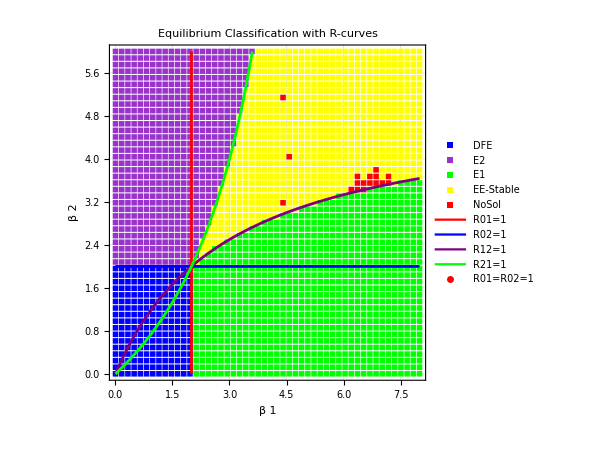

```mathematica
{R01,R02}=R0A/.E0;gridRes=50;plotInd={1,2};steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[(*Step 3:Scanning-now with mSi from step 1*)
{plot,noSol,results}=scan[RHS,var,par,coP,plotInd,mSi,(*mSi auto-provided*)gridRes,steTol,staTol,choTol,R01,R02,R12,R21];]
plot
```

```mathematica
Export["GavScan.pdf",plot]
```

GavScan.pdf